# Coronavirus

## Using data from Wolfram Data Repository

Source: https://datarepository.wolframcloud.com/resources/Novel-Coronavirus

Get the data from the repository:

```mathematica
data=ResourceData["Epidemic data for novel coronavirus 2019-nCoV from Wuhan, China"];
```

Sample the data:

```mathematica
RandomSample[%,3]
```

Make a country choropleth map for the data:

```mathematica
GeoRegionValuePlot[Normal@data[GroupBy["Country"],Total,#ConfirmedCases["LastValue"]&]]
```

-Graphics-

```mathematica
cases=data[Select[MemberQ[{Entity["AdministrativeDivision",{"Hubei","China"}],Entity["AdministrativeDivision",{"Zhejiang","China"}],Entity["AdministrativeDivision",{"Guangdong","China"}]},#AdministrativeDivision]&]][All,{"AdministrativeDivision","ConfirmedCases"}];
```

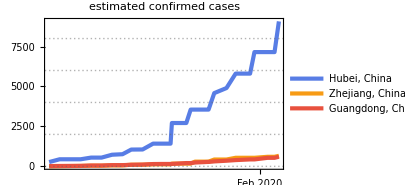

```mathematica
DateListPlot[Legended[#[[2]],#[[1]]]&/@cases,PlotTheme->"Business",PlotLabel->"estimated confirmed cases",ImageSize->300,PlotRange->Full]
```

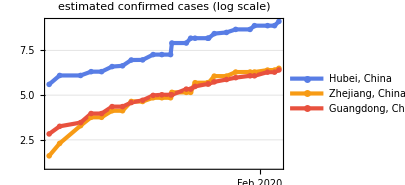

```mathematica
DateListLogPlot[Legended[#[[2]],#[[1]]]&/@cases,PlotTheme->"Business",PlotLabel->"estimated confirmed cases (log scale)",ImageSize->300,PlotRange->Full]
```

```mathematica
Export["D:\\git\\wolfram-coronavirus\\confirmed-cases.png",Out[13]]
```

D:\git\wolfram-coronavirus\confirmed-cases.png

```mathematica
Export["D:\\git\\wolfram-coronavirus\\confirmed-cases-log.png",Out[14]]
```

D:\git\wolfram-coronavirus\confirmed-cases-log.png

```mathematica
cases=data[Select[Not[MissingQ[#AdministrativeDivision]]&],{"AdministrativeDivision","ConfirmedCases"}];
```

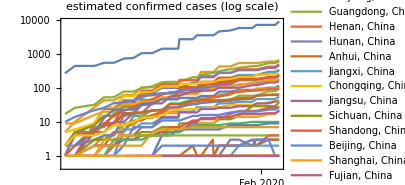

```mathematica
DateListLogPlot[Legended[#[[2]],#[[1]]]&/@cases,PlotLabel->"estimated confirmed cases (log scale)",ImageSize->300,PlotRange->Full]
```

#### wiki

```mathematica
results=WikidataSearch["coronavirus"]
```

{ExternalIdentifier[WikidataID,Q290805,<|Label→Coronavirus,Description→RNA virus|>]WikidataCoronavirushttp://www.wikidata.org/entity/Q290805,ExternalIdentifier[WikidataID,Q28200848,<|Label→Coronavirus as a possible cause of severe acute respiratory syndrome,Description→scientific article (publication date: 19 April 2003)|>]WikidataCoronavirus as a possible cause of severe acute respiratory syndromehttp://www.wikidata.org/entity/Q28200848,ExternalIdentifier[WikidataID,Q27641252,<|Label→Coronavirus main proteinase (3CLpro) structure: basis for design of anti-SARS drugs,Description→scientific article (publication date: 13 June 2003)|>]WikidataCoronavirus main proteinase (3CLpro) structure: basis for design of anti-SARS drugshttp://www.wikidata.org/entity/Q27641252,ExternalIdentifier[WikidataID,Q33694361,<|Label→Coronaviruses post-SARS: update on replication and pathogenesis.,Description→scientific article|>]WikidataCoronaviruses post-SARS: update on replication and pathogenesis.http://www.wikidata.org/entity/Q33694361,ExternalIdentifier[WikidataID,Q36369843,<|Label→Coronavirus infection of the central nervous system: host-virus stand-off.,Description→scientific article|>]WikidataCoronavirus infection of the central nervous system: host-virus stand-off.http://www.wikidata.org/entity/Q36369843,ExternalIdentifier[WikidataID,Q39545838,<|Label→Coronaviruses: structure and genome expression.,Description→scientific article published on December 1988|>]WikidataCoronaviruses: structure and genome expression.http://www.wikidata.org/entity/Q39545838,ExternalIdentifier[WikidataID,Q34132548,<|Label→Coronavirus spike proteins in viral entry and pathogenesis.,Description→scientific article|>]WikidataCoronavirus spike proteins in viral entry and pathogenesis.http://www.wikidata.org/entity/Q34132548,ExternalIdentifier[WikidataID,Q34193942,<|Label→Coronavirus pathogenesis and the emerging pathogen severe acute respiratory syndrome coronavirus.,Description→scientific article|>]WikidataCoronavirus pathogenesis and the emerging pathogen severe acute respiratory syndrome coronavirus.http://www.wikidata.org/entity/Q34193942,ExternalIdentifier[WikidataID,Q36801938,<|Label→Coronavirus transcription: subgenomic mouse hepatitis virus replicative intermediates function in RNA synthesis.,Description→scientific article published on March 1990|>]WikidataCoronavirus transcription: subgenomic mouse hepatitis virus replicative intermediates function in RNA synthesis.http://www.wikidata.org/entity/Q36801938,ExternalIdentifier[WikidataID,Q40603146,<|Label→Coronavirus replication complex formation utilizes components of cellular autophagy.,Description→scientific article published on 29 December 2003|>]WikidataCoronavirus replication complex formation utilizes components of cellular autophagy.http://www.wikidata.org/entity/Q40603146}

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q290805",<|"Label"->"Coronavirus","Description"->"RNA virus"|>]"Wikidata""Coronavirus"http://www.wikidata.org/entity/Q290805,"IdentifierProperties"]
```

{ExternalIdentifier[WikidataID,P486,<|Label→MeSH descriptor ID,Description→identifier for Descriptor or Supplementary concept in the Medical Subject Headings controlled vocabulary|>]WikidataMeSH descriptor IDhttp://www.wikidata.org/entity/P486,ExternalIdentifier[WikidataID,P508,<|Label→BNCF Thesaurus ID,Description→identifier in the subject indexing tool of the National Central Library of Florence|>]WikidataBNCF Thesaurus IDhttp://www.wikidata.org/entity/P508,ExternalIdentifier[WikidataID,P830,<|Label→Encyclopedia of Life ID,Description→eol.org item reference number|>]WikidataEncyclopedia of Life IDhttp://www.wikidata.org/entity/P830,ExternalIdentifier[WikidataID,P1296,<|Label→Gran Enciclopèdia Catalana ID,Description→identifier for an item in the Gran Enciclopèdia Catalana|>]WikidataGran Enciclopèdia Catalana IDhttp://www.wikidata.org/entity/P1296,ExternalIdentifier[WikidataID,P349,<|Label→National Diet Library Auth ID,Description→identifier for authority control per the National Diet Library of Japan|>]WikidataNational Diet Library Auth IDhttp://www.wikidata.org/entity/P349,ExternalIdentifier[WikidataID,P227,<|Label→GND ID,Description→identifier from an international authority file of names, subjects, and organizations (please don't use type n = name, disambiguation) - Deutsche Nationalbibliothek|>]WikidataGND IDhttp://www.wikidata.org/entity/P227,ExternalIdentifier[WikidataID,P1417,<|Label→Encyclopædia Britannica Online ID,Description→identifer for an article in the online version of Encyclopædia Britannica|>]WikidataEncyclopædia Britannica Online IDhttp://www.wikidata.org/entity/P1417,ExternalIdentifier[WikidataID,P3222,<|Label→NE.se ID,Description→ID of article on the Swedish Nationalencyklopedin (NE.se) site|>]WikidataNE.se IDhttp://www.wikidata.org/entity/P3222,ExternalIdentifier[WikidataID,P3827,<|Label→JSTOR topic ID,Description→identifier for a topic at JSTOR|>]WikidataJSTOR topic IDhttp://www.wikidata.org/entity/P3827,ExternalIdentifier[WikidataID,P4342,<|Label→Store norske leksikon ID,Description→identifier of an article in the online encyclopedia snl.no|>]WikidataStore norske leksikon IDhttp://www.wikidata.org/entity/P4342,ExternalIdentifier[WikidataID,P4527,<|Label→UK Parliament thesaurus ID,Description→Thesaurus of subject headings maintained by the libraries of the House of Commons and House of Lords in the UK. Covers around 110,000 topics (concepts, people, places, organisations, legislation, etc), with a structured taxonomy.|>]WikidataUK Parliament thesaurus IDhttp://www.wikidata.org/entity/P4527,ExternalIdentifier[WikidataID,P5055,<|Label→IRMNG ID,Description→identifier of a scientific name, in the Interim Register of Marine and Nonmarine Genera (IRMNG) database|>]WikidataIRMNG IDhttp://www.wikidata.org/entity/P5055}

```mathematica
properties=WikidataData[ExternalIdentifier["WikidataID","Q290805",<|"Label"->"Coronavirus","Description"->"RNA virus"|>]"Wikidata""Coronavirus"http://www.wikidata.org/entity/Q290805,"NonIdentifierProperties"]
```

{ExternalIdentifier[WikidataID,P18,<|Label→image,Description→image of relevant illustration of the subject; if available, use more specific properties (sample: coat of arms image, locator map, flag image, signature image, logo image, collage image); only images which exist on Wikimedia Commons are acceptable|>]Wikidataimagehttp://www.wikidata.org/entity/P18,ExternalIdentifier[WikidataID,P279,<|Label→subclass of,Description→all instances of these items are instances of those items; this item is a class (subset) of that item. Not to be confused with P31 (instance of)|>]Wikidatasubclass ofhttp://www.wikidata.org/entity/P279,ExternalIdentifier[WikidataID,P171,<|Label→parent taxon,Description→closest parent taxon of the taxon in question|>]Wikidataparent taxonhttp://www.wikidata.org/entity/P171,ExternalIdentifier[WikidataID,P225,<|Label→taxon name,Description→correct scientific name of a taxon (according to the reference given)|>]Wikidatataxon namehttp://www.wikidata.org/entity/P225,ExternalIdentifier[WikidataID,P373,<|Label→Commons category,Description→name of the Wikimedia Commons category containing files related to this item (without the prefix "Category:")|>]WikidataCommons categoryhttp://www.wikidata.org/entity/P373,ExternalIdentifier[WikidataID,P460,<|Label→said to be the same as,Description→this item is said to be the same as that item, but the statement is disputed|>]Wikidatasaid to be the same ashttp://www.wikidata.org/entity/P460,ExternalIdentifier[WikidataID,P31,<|Label→instance of,Description→that class of which this subject is a particular example and member|>]Wikidatainstance ofhttp://www.wikidata.org/entity/P31,ExternalIdentifier[WikidataID,P105,<|Label→taxon rank,Description→level in a taxonomic hierarchy|>]Wikidatataxon rankhttp://www.wikidata.org/entity/P105,ExternalIdentifier[WikidataID,P910,<|Label→topic's main category,Description→main Wikimedia category|>]Wikidatatopic's main categoryhttp://www.wikidata.org/entity/P910,ExternalIdentifier[WikidataID,P1889,<|Label→different from,Description→item that is different from another item, with which it is often confused|>]Wikidatadifferent fromhttp://www.wikidata.org/entity/P1889}

```mathematica
Import[First[WikidataData[ExternalIdentifier["WikidataID","Q290805",<|"Label"->"Coronavirus","Description"->"RNA virus"|>]"Wikidata""Coronavirus"http://www.wikidata.org/entity/Q290805,ExternalIdentifier["WikidataID","P18",<|"Label"->"image","Description"->"image of relevant illustration of the subject; if available, use more specific properties (sample: coat of arms image, locator map, flag image, signature image, logo image, collage image); only images which exist on Wikimedia Commons are acceptable"|>]"Wikidata""image"http://www.wikidata.org/entity/P18]]]
```

-Graphics-

```mathematica
Export["D:\\git\\wolfram-coronavirus\\coronavirus.png",Out[28]]
```

D:\git\wolfram-coronavirus\coronavirus.png

```mathematica
ExternalIdentifier["WikidataID","Q290805",<|"Label"->"Coronavirus","Description"->"RNA virus"|>]"Wikidata""Coronavirus"http://www.wikidata.org/entity/Q290805["Label"]
```

Coronavirus

```mathematica
ExternalIdentifier["WikidataID","Q290805",<|"Label"->"Coronavirus","Description"->"RNA virus"|>]"Wikidata""Coronavirus"http://www.wikidata.org/entity/Q290805["Label"]
```

```mathematica
ExternalIdentifier["WikidataID","Q290805",<|"Label"->"Coronavirus","Description"->"RNA virus"|>]"Wikidata""Coronavirus"http://www.wikidata.org/entity/Q290805["Description"]
```

RNA virus

```mathematica
ExternalIdentifier
```

```mathematica
ExternalIdentifier
```